```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
str = OpenRead["../../runs/Trials/40800763.dat"];
```

```mathematica
Close[str]
```

../../runs/Trials/40800763.dat

```mathematica
data2={};
```

```mathematica
Monitor[Do[
AppendTo[data2, First@ImportString[ReadLine[str], "Table"]];
, {k, 1, 10000}], ProgressIndicator[(k-1)/(10000-1)]]
```

```mathematica
data2
```

{}

```mathematica
$N = 9;$K=9; changeNK[$N, $K]
```

```mathematica
data = Import["../../runs/Trials/40800763.dat", "Table"];
```

```mathematica
rad=Monitor[
Table[radius[data[[k]]], {k, 1, Length[data]}],
ProgressIndicator[(k-1)/(Length[data]-1)]
]
```

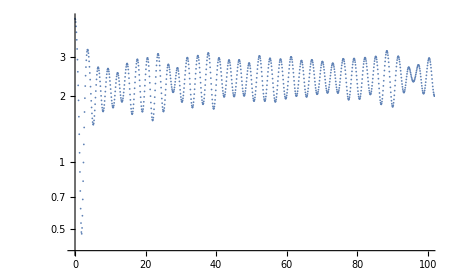

```mathematica
ListLogPlot[rad, PlotRange->{{000, 100}, Automatic}]
```

```mathematica
Mean@rad[[All, 2]]
```

2.55767

```mathematica
StandardDeviation@rad[[All, 2]]
```

0.218639

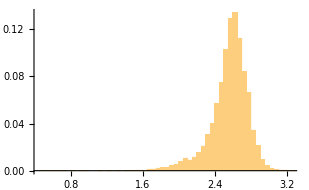

```mathematica
Histogram[rad[[All, 2]], 100, "Probability"]
```

```mathematica
energy[data[[4]]]
```

{0.3,1.+0. ⅈ}